## 2D AFHM: L = 4, N = 16

```mathematica
Remove["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Energies = Flatten[Import["energies2d.mat"]];
```

```mathematica
StableRanks = Flatten[Import["stableranks2d.mat"]];
```

```mathematica
E1 = NumberForm[Energies[[1]],20]
```

-11.22848320842886

```mathematica
m = 1.843282506017982
```

1.84328

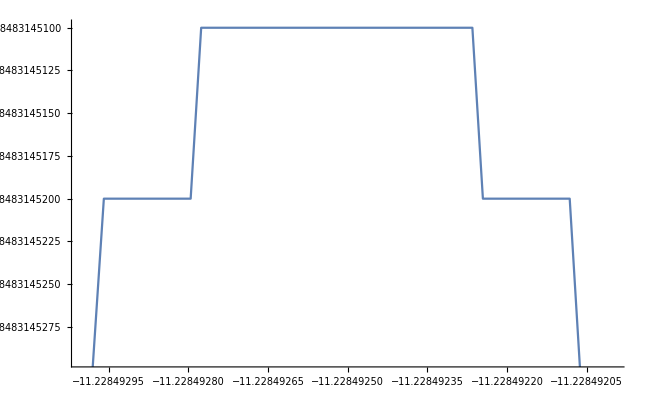

```mathematica
Plot[nu + (m Total[1/(StableRanks*(Energies-nu))])^(-1),{nu,-11.228493,-11.228492}]
```

```mathematica
(*choose broadening width*)sigma=0.1;
(*pick a fine grid over the energy range*)
energyGrid=Subdivide[Min[Energies],Max[Energies]+3 sigma,400];
```

```mathematica
(*original strong B/G/R palette*)paletteBGR={RGBColor[31/255,119/255,180/255],(*strong blue*)RGBColor[44/255,160/255,44/255],(*strong green*)RGBColor[214/255,39/255,40/255]    (*strong red*)};

(*darkening factor*)
darkFactor=0.95;

(*produce a darker version*)
palette=paletteBGR/. RGBColor[r_,g_,b_]:>RGBColor[darkFactor*r,darkFactor*g,darkFactor*b];
```

## FirstBlockPredicted

```mathematica
m =1.777778577875882;
nustar=Replace[nu,FindRoot[1/m*Total[1/(StableRanks*(Energies-nu)^2)]-(Total[1/(StableRanks*(Energies-nu))])^2,{nu,-11.228485},MaxIterations->200]];
```

```mathematica
NumberForm[nustar,20]
```

-11.22851767527875

```mathematica
uprobs = 1/(StableRanks*(Energies-nustar)^2);
probs = uprobs/Total[uprobs];
```

```mathematica
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))*Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
data1=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

## SecondBlockPredicted

```mathematica
m =1.843411886698179;
nustar=Replace[nu,FindRoot[1/m*Total[1/(StableRanks*(Energies-nu)^2)]-(Total[1/(StableRanks*(Energies-nu))])^2,{nu,-11.228492}]];
```

```mathematica
NumberForm[nustar,20]
```

-11.22849247009562

```mathematica
uprobs = 1/(StableRanks*(Energies-nustar)^2);
probs = uprobs/Total[uprobs];
```

```mathematica
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))*Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
data2=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

## ThirdBlockPredicted

```mathematica
m = 1.862545944586420;
nustar=Replace[nu,FindRoot[1/m*Total[1/(StableRanks*(Energies-nu)^2)]-(Total[1/(StableRanks*(Energies-nu))])^2,{nu,-11.228486}]];
```

```mathematica
NumberForm[nustar,20]
```

-11.22848537408168

```mathematica
uprobs = 1/(StableRanks*(Energies-nustar)^2);
probs = uprobs/Total[uprobs];
```

```mathematica
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))*Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
data3=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

## MakePlot

```mathematica
(*build custom y-ticks in the form 10^(-i)*)
ymin = - 20;
ymax=0;
yTicks=Table[{i,Superscript[10,i]},{i,-20,0,5}];
```

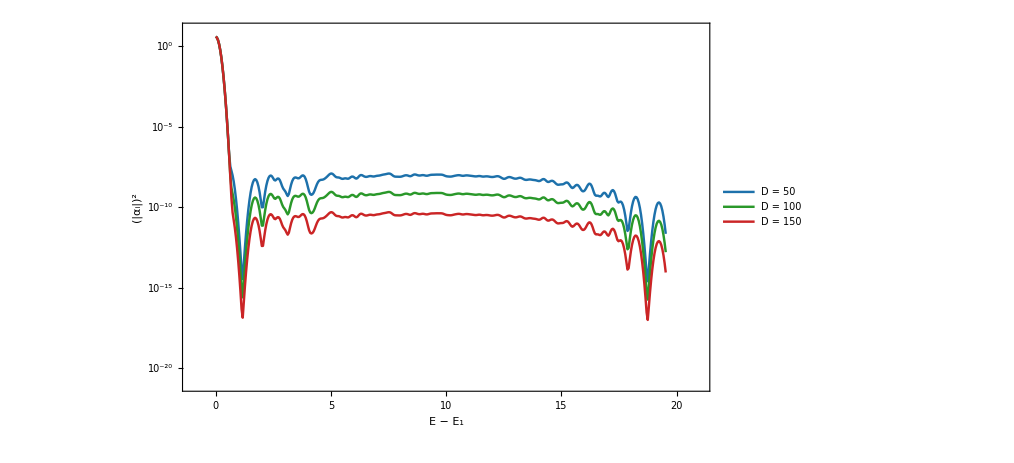

```mathematica
(*ymin=Floor[Min[data1[[All,2]]]];*)
tickLen={0.015,0};
ymin = - 20;
ymax=0;
yTicks=Table[{i,Superscript[10,i],tickLen},{i,-20,0,5}];
xTicks=Table[{i,i,tickLen},{i,0,20,5}];
xTicksAbove=Table[{i,"",tickLen},{i,0,15,5}];
yTicksRight = Table[{i,"",tickLen},{i,-20,-10,5}];

imgSize =750;
imagePadding={{120,10},{120,10}};

plotpredict=ListLinePlot[{data1,data2, data3},
PlotStyle->{{palette[[1]],AbsoluteThickness[1.75]},{palette[[2]],AbsoluteThickness[1.75]},{palette[[3]],AbsoluteThickness[1.75]}},
Frame->True,
FrameStyle->Directive[Black,AbsoluteThickness[2]],
Axes->False,
FrameTicks->{{yTicks,yTicksRight},{xTicks,xTicksAbove}},
FrameTicksStyle->Directive[AbsoluteThickness[2]],
FrameLabel->{{TraditionalForm[Superscript[Row[{"|",Subscript[α,i],"|"}],2]],None},{TraditionalForm[Row[{"E"," − ",Subscript["E",1]}]],None}},LabelStyle->{FontFamily->"Times",FontSize->30},
PlotTheme->"Detailed",
PlotRange->{{-1,21},{-21,1}},
GridLines->None,
PlotLegends->Placed[LineLegend[{"D = 50","D = 100","D = 150"},LegendFunction->(Framed[#,Background->White,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameMargins->{{8,15},{0,8}}]&),LegendMarkerSize->20,LegendLayout->"Column",LabelStyle->{FontFamily->"Times",FontSize->20}],Scaled[{0.91,0.85}]],
ImageSize->imgSize,ImagePadding->imagePadding
(*,Epilog->{AbsoluteThickness[1],Black,Line[{{1.71079522449159,ymin},{1.71079522449159,ymax}}]}*)
]
```

## FirstBlockActual

```mathematica
Clear[rho]
```

```mathematica
probs = Flatten[Import["psi0_2d_D50_noconserve_probs.mat"]];
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))*Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
actdata1=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

## SecondBlockActual

```mathematica
probs = Flatten[Import["psi0_2d_D100_noconserve_probs.mat"]];
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))*Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
actdata2=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

## ThirdBlockActual

```mathematica
probs = Flatten[Import["psi0_2d_D150_noconserve_probs.mat"]];
rho[x_]:=Total[probs*Table[(1/(sigma Sqrt[2 Pi]))*Exp[-(x-En)^2/(2 sigma^2)],{En,Energies}]];
SmoothedProbs = Table[rho[En],{En,energyGrid}];
actdata3=Transpose@{energyGrid-Min[Energies],Log10[SmoothedProbs]};
```

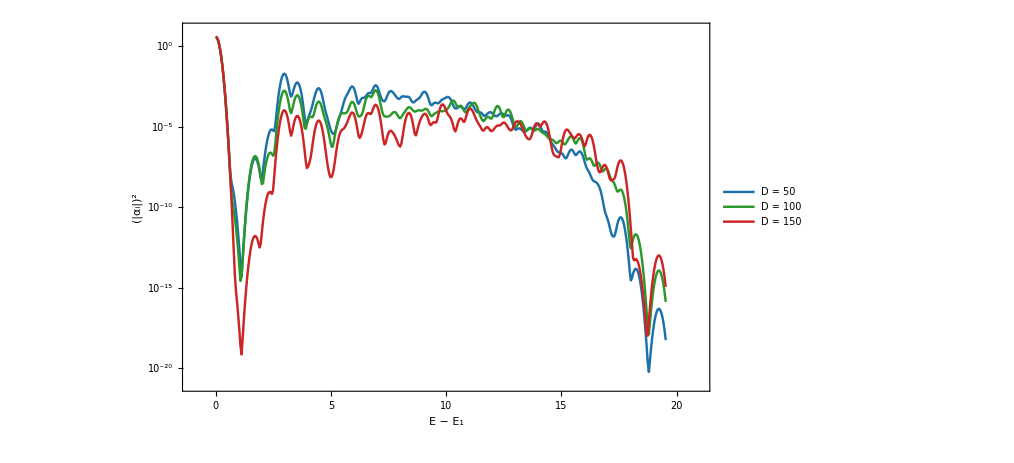

```mathematica
(*ymin=Floor[Min[data1[[All,2]]]];*)
tickLen={0.015,0};
ymin = - 20;
ymax=0;
yTicks=Table[{i,Superscript[10,i],tickLen},{i,-20,0,5}];
xTicks=Table[{i,i,tickLen},{i,0,20,5}];
xTicksAbove=Table[{i,"",tickLen},{i,0,15,5}];
yTicksRight = Table[{i,"",tickLen},{i,-20,-10,5}];

imgSize=750;
imagePadding={{120,10},{120,10}};

plotactual=ListLinePlot[{actdata1,actdata2,actdata3},
PlotStyle->{{palette[[1]],AbsoluteThickness[1.75]},{palette[[2]],AbsoluteThickness[1.75]},{palette[[3]],AbsoluteThickness[1.75]}},
Frame->True,
FrameStyle->Directive[Black,AbsoluteThickness[2]],
Axes->False,
FrameTicks->{{yTicks,yTicksRight},{xTicks,xTicksAbove}},
FrameTicksStyle->Directive[AbsoluteThickness[2]],
FrameLabel->{{TraditionalForm[Superscript[Row[{"|",Subscript[α,i],"|"}],2]],None},{TraditionalForm[Row[{"E"," − ",Subscript["E",1]}]],None}},LabelStyle->{FontFamily->"Times",FontSize->30},
PlotRange->{{-1,21},{-21,1}},
PlotTheme->"Detailed",
GridLines->None,
PlotLegends->Placed[LineLegend[{"D = 50", "D = 100", "D = 150"},LegendFunction->(Framed[#,Background->White,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameMargins->{{8,15},{0,8}}]&),LegendMarkerSize->20,LegendLayout->"Column",LabelStyle->{FontFamily->"Times",FontSize->20}],Scaled[{0.91,0.85}]],
ImageSize->imgSize,ImagePadding->imagePadding
(*,Epilog->{AbsoluteThickness[1],Black,Line[{{1.71079522449159,ymin},{1.71079522449159,ymax}}]}*)
]
```